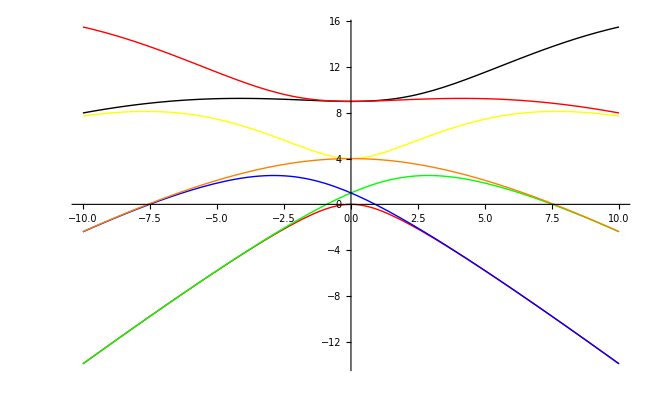

```mathematica
Plot[{MathieuCharacteristicA[0,q],MathieuCharacteristicA[1,q],MathieuCharacteristicB[1,q],MathieuCharacteristicA[2,q],MathieuCharacteristicB[2,q],MathieuCharacteristicA[3,q],MathieuCharacteristicB[3,q]},{q,-10,10},PlotStyle->{Red,Green,Blue,Yellow,Orange,Black}]
```

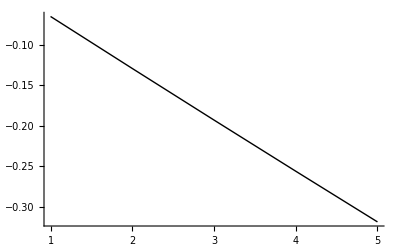

```mathematica
fx[n_,q_]:=(MathieuCharacteristicA[n,q]-MathieuCharacteristicA[0,q])/MathieuCharacteristicA[0,q];
ListPlot[Table[fx[n,1000],{n,1,5}],PlotStyle->{Red,Green,Blue,Yellow,Orange,Black},PlotRange->All,Joined->True]
```

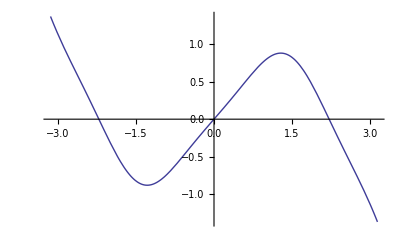

```mathematica
Plot[{Im[MathieuS[1,1,x]]},{x,-π,π}]
```

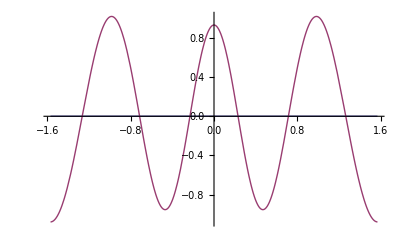

```mathematica
Plot[{0,Re[MathieuC[MathieuCharacteristicA[6,-5],-5,x]]},{x,-π/2,π/2},PlotRange->All]
```

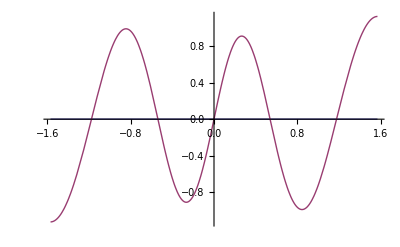

```mathematica
Plot[{0,MathieuS[MathieuCharacteristicB[5,-5],-5,x]},{x,-π/2,π/2},PlotRange->All]
```

```mathematica
N[MathieuS[MathieuCharacteristicB[2,-5],-5,π]]
```

-5.10118×10^-16+6.61744×10^-24 ⅈ

```mathematica
data=Import["POLLT40.dat"];
```

```mathematica
Clear[len];
len=Length[data]
```

1000

```mathematica
Clear[avgcorr11,avgcorr12,avgcorr21,avgcorr22];
Clear[errcorr11,errcorr12,errcorr21,errcorr22];
Clear[eval,eval1,eval2];
TMAX=10;
For[t=1,t≤TMAX,t++,
Clear[corr11,corr12,corr21,corr22];
corr11=Table[data[[n,2]],{n,t,500,10}];
corr12=Table[data[[n,3]],{n,t,500,10}];
corr21=Table[data[[n,4]],{n,t,500,10}];
corr22=Table[data[[n,5]],{n,t,500,10}];
avgcorr11[t]=Mean[corr11];
errcorr11[t]=Sqrt[StandardDeviation[corr11]/len];
avgcorr12[t]=Mean[corr12];
errcorr12[t]=Sqrt[StandardDeviation[corr12]/len];
avgcorr21[t]=Mean[corr21];
errcorr21[t]=Sqrt[StandardDeviation[corr21]/len];
avgcorr22[t]=Mean[corr22];
errcorr22[t]=Sqrt[StandardDeviation[corr22]/len];
]
(* Print the correlation matrix *)
For[t=1,t≤TMAX,t++,
(*Print[t," ",avgcorr11[t]," ",avgcorr12[t]," ",avgcorr21[t]," ",avgcorr22[t]];*)
Clear[mat];
mat={{avgcorr11[t],avgcorr12[t]},{avgcorr21[t],avgcorr22[t]}};
(*Print[MatrixForm[mat]];*)
eval=Eigenvalues[mat];
eval1[t]=eval[[1]];
eval2[t]=eval[[2]];
]
```

{0.000024999,6.2497×10^-10,1.5624×10^-14,3.9059×10^-19,9.7644×10^-24,2.441×10^-28,6.1024×10^-33,1.5256×10^-37,3.8138×10^-42,9.5344×10^-47}

{1.5624×10^-10,2.4412×10^-20,3.8143×10^-30,5.9597×10^-40,9.3117×10^-50,1.4549×10^-59,2.2732×10^-69,3.5518×10^-79,5.5495×10^-89,8.6707×10^-99}

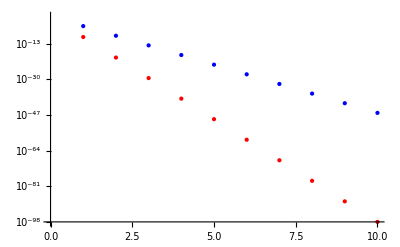

```mathematica
e1=Table[eval1[t],{t,1,10}]
e2=Table[eval2[t],{t,1,10}]
ListLogPlot[{e1,e2},PlotStyle->{{PointSize[Large],Blue},{PointSize[Large],Red}}]
```

```mathematica
For[i=1,i<TMAX,i++,
Print[i," ",Log[eval1[i]/eval1[i+1]]," ",Log[eval2[i]/eval2[i+1]]];
]
```

1 10.5966 22.5796

2 10.5967 22.5796

3 10.5967 22.5796

4 10.5967 22.5796

5 10.5967 22.5796

6 10.5967 22.5796

7 10.5966 22.5796

8 10.5967 22.5796

9 10.5966 22.5796

```mathematica
(BesselI[1,0.01]/BesselI[0,0.01])*(BesselI[-1,0.01]/BesselI[0,0.01])*(BesselI[1,0.02]/BesselI[0,0.02])
```

2.49981×10^-7

```mathematica
(* For the free case, when the oscillators are not coupled *)
Clear[data,c1,c2,c3,m1,m2,m3];
data=Import["test.dat"];
```

```mathematica
data[[1,1]]
```

{1,0.000024999,1.5624×10^-10,4.3401×10^-16}

```mathematica
c1=Table[data[[n,2]],{n,1,10}];
c2=Table[data[[n,3]],{n,1,10}];
c3=Table[data[[n,4]],{n,1,10}];
```

```mathematica
For[i=1,i<10,i++,
m1[i]=Log[c1[[i]]/c1[[i+1]]];
m2[i]=Log[c2[[i]]/c2[[i+1]]];
m3[i]=Log[c3[[i]]/c3[[i+1]]];
Print[i," ",Log[c1[[i]]/c1[[i+1]]]," ",Log[c2[[i]]/c2[[i+1]]]," ",Log[c3[[i]]/c3[[i+1]]]];
Print[i," ",m2[i]/m1[i]," ",m3[i]/m1[i]];
]
```

1 5.99397 13.3726 21.5617

1 2.231 3.59723

2 5.99399 13.3725 21.5616

2 2.23099 3.59721

3 5.99394 13.3726 21.5617

3 2.23101 3.59724

4 5.99396 13.3726 21.5617

4 2.23101 3.59724

5 5.99396 13.3726 21.5616

5 2.23101 3.59723

6 5.99397 13.3726 21.5616

6 2.231 3.59722

7 5.99395 13.3725 21.5617

7 2.23101 3.59724

8 5.99397 13.3726 21.5616

8 2.231 3.59722

9 5.99396 13.3726 21.5617

9 2.231 3.59723